## AbstractCategory ReducedMorphismAssociation

Here, y•f = h•(g•f) = h•x, but the older ResourceFunction[“AbstractCategory”] doesn’t know this (some morphisms appear double) because it can’t handle non-elementary composition equivalences.

```mathematica
cat=ResourceFunction["AbstractCategory"][<|f->{a,b},g->{b,c},h->{c,d},i->{d,e},x->{a,c},y->{b,d}|>,{},{CircleDot[g,f]==x,CircleDot[h,g]==y}];
cat["ReducedMorphismAssociation"]
cat["ReducedLabeledGraph"]
```

GraphElementData::shdw: Symbol GraphElementData appears in multiple contexts {System`,Global`}; definitions in context System` may shadow or be shadowed by other definitions.

$Failed[Association[f→{a,b},g→{b,c},h→{c,d},i→{d,e},x→{a,c},y→{b,d}],{},{g⊙f==x,h⊙g==y}][ReducedMorphismAssociation]

$Failed[Association[f→{a,b},g→{b,c},h→{c,d},i→{d,e},x→{a,c},y→{b,d}],{},{g⊙f==x,h⊙g==y}][ReducedLabeledGraph]

{f→a->b,g→b->c,h→c->d,i→d->e,x→a->c,h⊙g→b->d,(h⊙g)⊙f→a->d,i⊙h→c->e,i⊙y→b->e,i⊙(h⊙(g⊙f))→a->e,ã→a->a,b̃→b->b,c̃→c->c,d̃→d->d,ẽ→e->e}

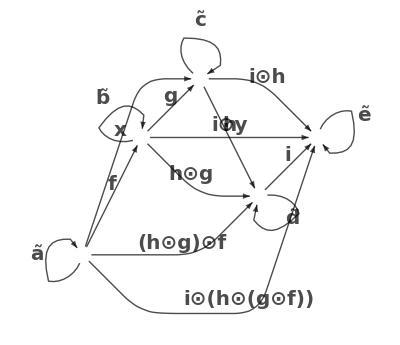

```mathematica
cat=AbstractCategory[<|f->{a,b},g->{b,c},h->{c,d},i->{d,e},x->{a,c},y->{b,d}|>,{},{CircleDot[g,f]==x,CircleDot[h,g]==y}];
cat["ReducedMorphismAssociation"]
cat["ReducedLabeledGraph"]
```

ReducedMorphismAssociation still treats no two morphisms as equivalent a priori when objects are reduced, except for identities, which get merged too.

AbstractCategory[…]

{f→A2->B3,g→B3->B3,h→A2->B3,i→B3->B3,g⊙f→A2->B3,i⊙g→B3->B3,i⊙h→A2->B3,i⊙(g⊙f)→A2->B3,OverTilde[A2]→A2->A2,OverTilde[B3]→B3->B3}

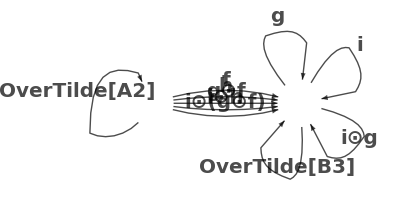

```mathematica
cat2=AbstractCategory[<|f->{A,B},g->{B,B2},h->{A2,B2},i->{B2,B3}|>,{A==A2,B==B2,B3==B2}]
cat2["ReducedMorphismAssociation"]
cat2["ReducedLabeledGraph"]
```

Compatibility with CommutativityEquations (if they are correct anyway):

```mathematica
cEq=cat2["ReducedCommutativityEquations"]
```

{f==h,f==g⊙f,f==i⊙h,f==(i⊙g)⊙f,g==i,g==i⊙g,g==OverTilde[B2]}

AbstractCategory[…]

{i⊙(g⊙f)→A2->B3,OverTilde[B3]→B3->B3,OverTilde[A2]→A2->A2}

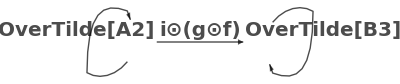

```mathematica
cat3=AbstractCategory[<|f->{A,B},g->{B,B2},h->{A2,B2},i->{B2,B3}|>,{A==A2,B==B2,B3==B2},cEq]
cat3["ReducedMorphismAssociation"]
cat3["ReducedLabeledGraph"]
```

Functor test from Issue #4 (make sure to use the updated AbstractFunctor code, which uses the new AbstractCategory):

```mathematica
cat=AbstractCategory[<|f->{U,V},g->{V,X},h->{Y,X},i->{X,Z}|>];
func=AbstractFunctor[cat,<|U->A,Y->A2,V->B,X->B2,Z->B3|>,<||>,{},<||>,CircleDot,OverTilde,{A==A2,B==B2,B2==B3},{CircleDot[g,f]==f,CircleDot[i,h]==h,h==f,CircleDot[i,g]==OverTilde[B3],g==OverTilde[B3],i==OverTilde[B3]}];
func["CodomainCategory"]["ReducedMorphismAssociation"]
func["CodomainCategory"]["ReducedLabeledGraph"]
```

{i⊙(g⊙f)→A2->B3,OverTilde[B3]→B3->B3,OverTilde[A2]→A2->A2}

-Graphics-

<|f→A2->B3,OverTilde[B3]→B3->B3,OverTilde[B3]⊙f→A2->B3,OverTilde[A2]→A2->A2|>

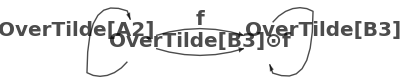

```mathematica
cat=ResourceFunction["AbstractCategory"][<|f->{U,V},g->{V,X},h->{Y,X},i->{X,Z}|>];
func=ResourceFunction["AbstractFunctor"][cat,<|U->A,Y->A2,V->B,X->B2,Z->B3|>,<||>,{},<||>,CircleDot,OverTilde,{A==A2,B==B2,B2==B3},{CircleDot[g,f]==f,CircleDot[i,h]==h,h==f,CircleDot[i,g]==OverTilde[B3],g==OverTilde[B3],i==OverTilde[B3]}];
func["CodomainCategory"]["ReducedMorphismAssociation"]
func["CodomainCategory"]["ReducedLabeledGraph"]
```

Github Issue #4 exact testcase:

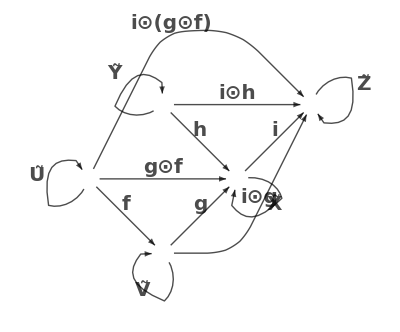
-Graphics-→-Graphics-

```mathematica
cat=AbstractCategory[<|f->{U,V},g->{V,X},h->{Y,X},i->{X,Z}|>];
func=AbstractFunctor[cat,<|U->A,Y->A2,V->B,X->B2,Z->B3|>,<||>,{},<||>,CircleDot,OverTilde,{A==A2,B==B2,B2==B3},{f==h,CircleDot[g,f]==f,CircleDot[i,h]==h,CircleDot[i,g]==OverTilde[B3],i==g,g==OverTilde[B3]}];
func["ReducedLabeledGraph"]
```

```mathematica
cat=AbstractCategory[<|f->{U,V},g->{V,X},h->{Y,X},i->{X,Z}|>];
func=AbstractFunctor[cat,<|U->A,Y->A2,V->B,X->B2,Z->B3|>,<||>,{},<||>,CircleDot,OverTilde,{A==A2,B==B2,B2==B3},{f==h,CircleDot[g,f]==f,CircleDot[i,h]==h,CircleDot[i,g]==OverTilde[B3],i==g,OverTilde[B3]==g}];
func["ReducedLabeledGraph"]
```

-Graphics-→-Graphics-

## AbstractFunctor MorphismMappings

Github issue #5 example

```mathematica
cat=AbstractCategory[<|f->{U,V},g->{V,W}|>];
func=AbstractFunctor[cat,<|U->A,V->B,W->B|>,<||>,{},<||>];
func["MorphismMappings"]
```

Thread::tdlen: Objects of unequal length in {f,g,g⊙f,Ũ,Ṽ,W̃}→{f,Ã,B̃} cannot be combined.

<|{f,g,g⊙f,Ũ,Ṽ,W̃}→{f,Ã,B̃}|>

Workaround using imposed equivalences instead:

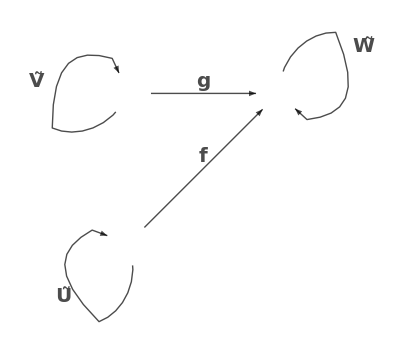
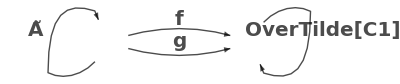
-Graphics-→-Graphics-

<|f→f,g→g,Ũ→Ã,W̃→OverTilde[C1],Ṽ→Ã|>

```mathematica
cat=AbstractCategory[<|f->{U,W},g->{V,W}|>];
func=AbstractFunctor[cat,<|U->A,V->B,W->C1|>,<||>,{},<||>,CircleDot,OverTilde,{A==B}];
func["ReducedLabeledGraph"]
func["ReducedMorphismMappings"]
```

```mathematica
cat=AbstractCategory[<|f->{U,V},g->{V,X},h->{Y,X},i->{X,Z}|>];
func=AbstractFunctor[cat,<|U->A,Y->A2,V->B,X->B2,Z->B3|>,<||>,{},<||>,CircleDot,OverTilde,{A==A2,B==B2,B2==B3},{f==h,CircleDot[g,f]==f,CircleDot[i,h]==h,CircleDot[i,g]==OverTilde[B3],i==g,OverTilde[B3]==g}];
func["ReducedLabeledGraph"]
func["ReducedMorphismMappings"]
```

-Graphics-→-Graphics-

<|f→i⊙(g⊙f),g→OverTilde[B3],h→i⊙(g⊙f),i→OverTilde[B3],g⊙f→i⊙(g⊙f),i⊙g→OverTilde[B3],i⊙h→i⊙(g⊙f),i⊙(g⊙f)→i⊙(g⊙f),Ũ→OverTilde[A2],Ṽ→OverTilde[B3],X̃→OverTilde[B3],Ỹ→OverTilde[A2],Z̃→OverTilde[B3]|>

## AbstractFunctor CartesianMorphisms

n.b. the non-injective mapping (even of morphisms) is still not working, so you need to go via the reduced morphism list

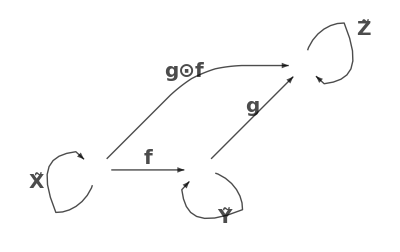
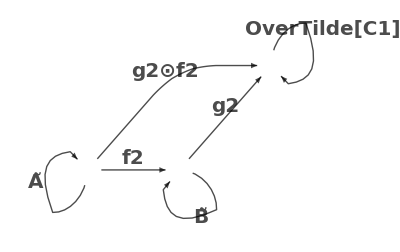
-Graphics-→-Graphics-

<|f→f2,g→g2,g⊙f→g2⊙f2,X̃→Ã,Ỹ→B̃,Z̃→OverTilde[C1]|>

{f→X->Y,g→Y->Z,g⊙f→X->Z,X̃→X->X,Ỹ→Y->Y,Z̃→Z->Z}

{x,{X,Ã→A->A}}

{X̃→X->X}

{x,{Y,f2→A->B}}

{f→X->Y}

{x,{Y,B̃→B->B}}

{Ỹ→Y->Y}

{x,{Z,g2→B->C1}}

{g→Y->Z}

{x,{Z,g2⊙f2→A->C1}}

{g⊙f→X->Z}

{x,{Z,OverTilde[C1]→C1->C1}}

{Z̃→Z->Z}

True

```mathematica
func=AbstractFunctor[AbstractCategory[<|f->{X,Y},g->{Y,Z}|>],<|X->A,Y->B,Z->C1|>,<|g->g2,f->f2,h->h2|>,{},<||>,{},{f2==h2}];
func["ReducedLabeledGraph"]
func["ReducedMorphismMappings"]
func["CartesianMorphisms"]
func["GrothendieckFibrationQ"]
```

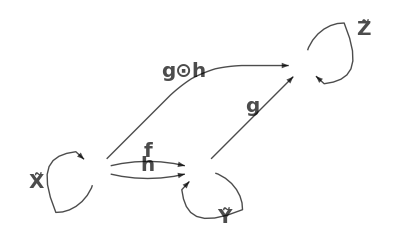
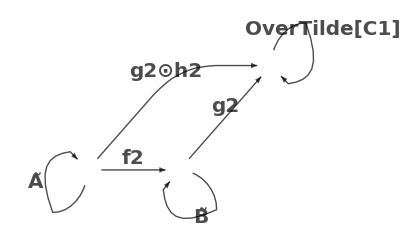
-Graphics-→-Graphics-

<|f→f2,g→g2,h→f2,g⊙h→g2⊙h2,X̃→Ã,Ỹ→B̃,Z̃→OverTilde[C1]|>

{f→X->Y,h→X->Y,g⊙h→X->Z,X̃→X->X,Ỹ→Y->Y,Z̃→Z->Z}

{x,{X,Ã→A->A}}

{X̃→X->X}

{x,{Y,f2→A->B}}

{f→X->Y,h→X->Y}

{x,{Y,B̃→B->B}}

{Ỹ→Y->Y}

{x,{Z,g2→B->C1}}

{}

{x,{Z,g2⊙h2→A->C1}}

{g⊙h→X->Z}

{x,{Z,OverTilde[C1]→C1->C1}}

{Z̃→Z->Z}

False

```mathematica
func=AbstractFunctor[AbstractCategory[<|f->{X,Y},g->{Y,Z},h->{X,Y}|>,{},{CircleDot[g,f]==CircleDot[g,h]}],<|X->A,Y->B,Z->C1|>,<|g->g2,f->f2,h->h2|>,{},<||>,{},{f2==h2}];
func["ReducedLabeledGraph"]
func["ReducedMorphismMappings"]
func["CartesianMorphisms"]
func["GrothendieckFibrationQ"]
```

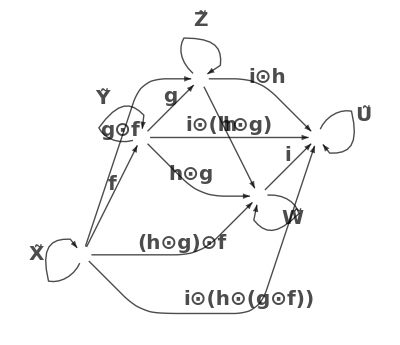
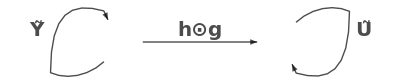
-Graphics-→-Graphics-

<|f→Ỹ,g→h⊙g,h→Ũ,i→Ũ,g⊙f→h⊙g,h⊙g→h⊙g,i⊙h→Ũ,(h⊙g)⊙f→h⊙g,i⊙(h⊙g)→h⊙g,i⊙(h⊙(g⊙f))→h⊙g,X̃→Ỹ,Ỹ→Ỹ,Z̃→Ũ,W̃→Ũ,Ũ→Ũ|>

False

{f→X->Y,g→Y->Z,h→Z->W,i→W->U,g⊙f→X->Z,h⊙g→Y->W,i⊙h→Z->U,(h⊙g)⊙f→X->W,i⊙(h⊙g)→Y->U,i⊙(h⊙(g⊙f))→X->U,X̃→X->X,Ỹ→Y->Y,Z̃→Z->Z,W̃→W->W,Ũ→U->U}

{x,{X,Ỹ→Y->Y}}

{X̃→X->X}

{x,{Y,Ỹ→Y->Y}}

{f→X->Y,Ỹ→Y->Y}

{x,{Z,h⊙g→Y->U}}

{g→Y->Z,g⊙f→X->Z}

{x,{Z,Ũ→U->U}}

{Z̃→Z->Z}

{x,{W,h⊙g→Y->U}}

{h⊙g→Y->W,(h⊙g)⊙f→X->W}

{x,{W,Ũ→U->U}}

{h→Z->W,W̃→W->W}

{x,{U,h⊙g→Y->U}}

{i⊙(h⊙g)→Y->U,i⊙(h⊙(g⊙f))→X->U}

{x,{U,Ũ→U->U}}

{i→W->U,i⊙h→Z->U,Ũ→U->U}

True

```mathematica
func=AbstractFunctor[AbstractCategory[<|f->{X,Y},g->{Y,Z},h->{Z,W},i->{W,U}|>],<||>,<||>,{},<||>,{X==Y,W==U,Z==W},{i==OverTilde[U],f==OverTilde[Y],h==OverTilde[U],CircleDot[OverTilde[U],OverTilde[U]]==OverTilde[U],g==CircleDot[h,g],CircleDot[h,CircleDot[g,f]]==CircleDot[h,g],CircleDot[i,CircleDot[h,CircleDot[g,f]]]==CircleDot[h,g]}];
func["ReducedLabeledGraph"]
func["ReducedMorphismMappings"]
func["DiscreteFibrationQ"]
func["CartesianMorphisms"]
func["GrothendieckFibrationQ"]
```

```mathematica
func=AbstractFunctor[AbstractCategory[<|f->{X,Y},g->{Y,Z},h->{Y,W},i->{Z,U},j->{Z,W}|>,{U==W},{CircleDot[i,g]==h,CircleDot[j,g]==h}],<|X->A,Y->B|>,<|f->F,g->G|>,{Q,V},<|k->{Q,V},l->{Z,Q}|>,CircleTimes,OverBar,{Q==V},{CircleTimes[l,G]==CircleTimes[CircleTimes[k,l],G]}];
func["ReducedLabeledGraph"]
func["ReducedMorphismMappings"]
func["DiscreteFibrationQ"]
func["CartesianMorphisms"]
func["GrothendieckFibrationQ"]
```

AbstractFunctor[AbstractCategory[<|f→{X,Y},g→{Y,Z},h→{Y,W},i→{Z,U},j→{Z,W}|>,{U==W},{i⊙g==h,j⊙g==h}],<|X→A,Y→B|>,<|f→F,g→G|>,{Q,V},<|k→{Q,V},l→{Z,Q}|>,CircleTimes,OverBar,{Q==V},{l⊗G==(k⊗l)⊗G}][ReducedLabeledGraph]